Define the surface interesctions
y direction along the cyl
x axis of tilt
surface of the mcp
z=y cos[α]/Sin[α]
parametric cyl (u,v)
y=v
x=Cos[u]
z=Sin[u]
the intersection is thus
y=z Sin[α]/Cos[α]=Sin[u] Sin[α]/Cos[α]
x=Cos[u]
z=Sin[u]
Rotate into the plane of the mcp x’,y’,z’
x’=Cos[u]
y’=(Sin[u] Sin[α]/Cos[α])Cos[α]-(Sin[u])Sin[α]
z’=(Sin[u] Sin[α]/Cos[α])Sin[α]+(Sin[u])Cos[α]
simplify
x’=Cos[u]
y’=0
z’= (Sin[u] (Sin[α])^2)/Cos[α]+Sin[u]Cos[α]

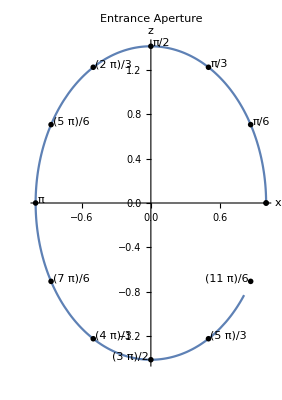

```mathematica
xpos[u_]=Cos[u];
zpos[u_]=(Sin[u] (Sin[α])^2)/Cos[α]+Sin[u]Cos[α];
w=0.1;
alphaTemp=45*π/180;

Show[
ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,0π,1.8π},AxesLabel->{"x","z"},PlotLabel->"Entrance Aperture"],
ListPlot[Table[Labeled[{xpos[a],zpos[a]},a],{a,0,2Pi,Pi/6}]/.α->alphaTemp,
PlotStyle->Black,PlotMarkers->{Automatic,Medium}]/.Line->Point,
PlotRangePadding->0.2
]
```

Now try to solve for the intersection points of two of these eclipse with one offset in z

```mathematica
alphaTemp=45*π/180;
Manipulate[Show[ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,-π,π},PlotLabel->b,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ParametricPlot[{xpos[a],zpos[a]+b}/.α->alphaTemp,{a,-π,π},AxesLabel->{"x","z"},PlotLabel->b]],{b,-0.1,3}]
```

```mathematica
intersectionpts=Solve[{xpos[u]==xpos[q], 
zpos[u]==zpos[q]+d},{q,u}]
```

{{q→ConditionalExpression[ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[1],C[1]∈ℤ],u→ConditionalExpression[ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),d/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[2],C[2]∈ℤ]},{q→ConditionalExpression[ArcTan[(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[1],C[1]∈ℤ],u→ConditionalExpression[ArcTan[(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),d/(2 (Cos[α]+Sin[α] Tan[α]))]+2 π C[2],C[2]∈ℤ]}}

Remove the 2π periodicity in the solution

```mathematica
Intersect1=intersectionpts[[2,1,2]]/.C[1]->0
Intersect2=intersectionpts[[1,1,2]]/.C[1]->0
```

ArcTan[(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))]

ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))]

Show that they are symetric

```mathematica
N[Intersect1/.{α-> 0.1,C[1]->0,d->0.5},1]
N[Intersect2/.{α-> 0.1,C[1]->0,d->0.5},1]+π
```

-0.251391

0.251391

```mathematica
alphaTemp=45*π/180;
Manipulate[Show[ParametricPlot[{xpos[a],zpos[a]}/.α->alphaTemp,{a,-π,π},PlotLabel->StringForm["``.,``.,``.",b,N[Intersect1/.{α->alphaTemp,d->b},2],N[Intersect2/.{α->alphaTemp,d->b},2]],
PlotRange->{{-1.5,1.5},{-1.5,1.5}}],ParametricPlot[{xpos[a],zpos[a]+b}/.α->alphaTemp,{a,-π,π}],
ListPlot[{{xpos[Intersect1],zpos[Intersect1]+d},{xpos[Intersect2],zpos[Intersect2]+d}}/.{α->alphaTemp,d->b},PlotStyle->Red]
],{b,-0.1,3}]
```

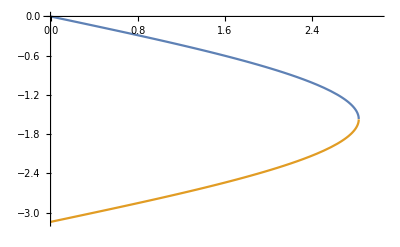

```mathematica
Plot[{Intersect1/.{α->alphaTemp,d->b},Intersect2/.{α->alphaTemp,d->b}},{d,0,3}]
```

Now for some displacement of the moving ellipse find the arclength that remains in the stationary elipse ,
we use the simple formula
∫√((dx/du)^2+(dy/dy)^2)du
find the indefinite integral and have a look at the discontinuities

```mathematica
√((xpos'[u])^2+(zpos'[u])^2)
```

√(Sin[u]^2+(Cos[u] Cos[α]+Cos[u] Sin[α] Tan[α])^2)

```mathematica
ArcLenIndef=Integrate[√((xpos'[u])^2+(zpos'[u])^2),u]
```

(√(-(-6-2 Cos[2 u]+Cos[2 (u-α)]-2 Cos[2 α]+Cos[2 (u+α)]) Sec[α]^2) (1/(√((Cos[α]+ⅈ Sin[α])^2))ⅈ (-2 Cos[α] EllipticF[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[u/2]],Cos[4 α]-ⅈ Sin[4 α]]+EllipticE[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[u/2]],Cos[4 α]-ⅈ Sin[4 α]] (Cos[α]+ⅈ Sin[α])) (Cos[α]+ⅈ Sin[α]) √(1+Cos[2 α] Tan[u/2]^2-ⅈ Sin[2 α] Tan[u/2]^2) √(1+Cos[2 α] Tan[u/2]^2+ⅈ Sin[2 α] Tan[u/2]^2)+Cos[u/2]^2 (Tan[u/2]+2 Cos[2 α] Tan[u/2]^3+Tan[u/2]^5)))/((1+Cos[u]) √(-(-6-2 Cos[2 u]+Cos[2 (u-α)]-2 Cos[2 α]+Cos[2 (u+α)])/(1+Cos[u])^2) √(1+2 Cos[2 α] Tan[u/2]^2+Tan[u/2]^4))

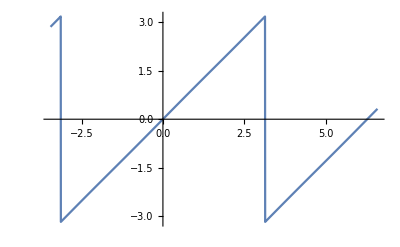

```mathematica
Plot[ArcLenIndef/.{u->x,α->12*π/180},{x,-1.1π,2.1π}]
```

Trying to keep between these discontinuities we chose -π<u<0 which also happens to be the range of the intersect coordinates under positive d displacement of the moving elipse

```mathematica
assum={α∈Reals,α>0,u<0,u>-π,d∈ Reals,d>0};
```

```mathematica
ArcLenIndef=Integrate[√((xpos'[u])^2+(zpos'[u])^2),u,Assumptions->assum]
```

(√(-(-6-2 Cos[2 u]+Cos[2 (u-α)]-2 Cos[2 α]+Cos[2 (u+α)]) Sec[α]^2) (1/(√((Cos[α]+ⅈ Sin[α])^2))ⅈ (-2 Cos[α] EllipticF[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[u/2]],Cos[4 α]-ⅈ Sin[4 α]]+EllipticE[ⅈ ArcSinh[√((Cos[α]+ⅈ Sin[α])^2) Tan[u/2]],Cos[4 α]-ⅈ Sin[4 α]] (Cos[α]+ⅈ Sin[α])) (Cos[α]+ⅈ Sin[α]) √(1+Cos[2 α] Tan[u/2]^2-ⅈ Sin[2 α] Tan[u/2]^2) √(1+Cos[2 α] Tan[u/2]^2+ⅈ Sin[2 α] Tan[u/2]^2)+Cos[u/2]^2 (Tan[u/2]+2 Cos[2 α] Tan[u/2]^3+Tan[u/2]^5)))/((1+Cos[u]) √(-(-6-2 Cos[2 u]+Cos[2 (u-α)]-2 Cos[2 α]+Cos[2 (u+α)])/(1+Cos[u])^2) √(1+2 Cos[2 α] Tan[u/2]^2+Tan[u/2]^4))

Try to do the definite integral directly

```mathematica
ustart=Intersect1;
uend=Intersect2;
Integrate[√((xpos'[u])^2+(zpos'[u])^2),{u,ustart,uend},Assumptions->{assum,ustart<0,ustart>-π,uend<0,uend>-π}]
```

$Aborted

Try to do it manually

```mathematica
ArcLenDefManual=ArcLenIndef/.u->Intersect2-ArcLenIndef/.u->Intersect1
```

(√(-(6+Cos[2 (α+ArcTan[-1/1,1]-(1 ((ⅈ 3 √(1+Cos[2 α] 1^2+ⅈ Sin[2 α] Tan[1]^2))/(√((Cos[α]+ⅈ 1)^2))+Cos[1/2 1]^2 (Tan[1/2 1]+1+1^5)))/(√(-(-6-2 Cos[2 α]-2 1+Cos[2 1]+Cos[2 (α+ArcTan[1,-d/1])])/(1+(√1)/1)^2) 1 √(1+2 Cos[1] (Tan11])^2+Tan[1/2 1]^4)))]) 1^2) (1))/((1+Cos[ArcTan[-(√(-d^2+4 Cos[α]^2+8 Sin[α]^2+4 Sin[α]^2 Tan[α]^2))/(2 √(Cos[α]^2+2 Sin[α]^2+Sin[α]^2 Tan[α]^2)),-d/(2 (Cos[α]+Sin[α] Tan[α]))]-(√(-(-6-2 Cos[2 α]-2 1+Cos[2 (1)]+Cos[2 (α+ArcTan[(√(-d^2+2+1))/(2 √1),-d/(2 1)])]) 1) 1)/(√(-(-6-2 1-1+1+Cos[2 (α+ArcTan[1])])/(1+1)^2) (1+1) √(1+2 Cos[2 α] 1^2+Tan[1/2 1]^4))]) √1 √(1+2 1 1^2+1^4))
 |  |  |  |

Now simplify down this big mess

```mathematica
ArcLenDefManual=Simplify[ArcLenDefManual,Assumptions->assum,TimeConstraint->6000]
```

Simplify::time: Time spent on a transformation exceeded 600. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
ArcLenDefManual=Simplify[Expand[ArcLenDefManual],Assumptions->assum]
```

The expression for this integral is way to big and it wont simplify down

```mathematica
Integrate[ArcLenDefManual,d]
```

$Aborted

## Approx Solution

From looking at the distribution of distances in numerical sim (see matlab) I have guessed that the distribution is of the form
ρ(len)=√(lenmax^2-len^2)
when normalization is done carefully numerical simulations give this distribution within the simulation noise.
Perhaps this can inspire a different approach to its proof.

Here I want to calculate the variance and mean of this distribution.

```mathematica
Integrate[√(r^2-x^2),{x,0,r}]
```

1/4 π r √(r^2)

```mathematica
mean=Integrate[x(√(r^2-x^2))/(1/4 π r √(r^2)),{x,0,r}]
N[mean/.r->1]
```

(4 r)/(3 π)

0.424413

```mathematica
var=Integrate[(x-mean)^2(√(r^2-x^2))/(1/4 π r^2),{x,0,r},Assumptions->{Im[r]==0,r>0}]
```

1/36 (9-64/π^2) r^2

```mathematica
N[√(var/.r->1)]
```

0.264336

```mathematica
4./3 π
```

4.18879